## Viscous Dragging

```mathematica
precompute[positions_,perturbedIndex_,s_,ν_, θ_]:= Block[
{
dp = Differences[positions],
betaList,
diffs,
reducedAngles
},
betaList =ArcTan@@@ Join[-dp[[1;;perturbedIndex-1]],dp[[perturbedIndex;;-1]]] ;
reducedAngles=θ +2 ArcCot[ⅇ^(-s+s ν)Cot[(betaList-θ)/2]];
reducedAngles=Insert[reducedAngles,θ,perturbedIndex];
Transpose@{Cos[reducedAngles],Sin[reducedAngles]}]
```

```mathematica
displacements[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
Block[{newPositions,betaList,Δ  },
Δ=precompute[positionList,perturbedIndex,s,ν,θ];
newPositions[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];
newPositions[index_] := newPositions[index]=
Module[{nextIndex=index-Sign[index-perturbedIndex]},
newPositions[nextIndex] + Δ[[index]]
];
newPositions/@Range[Length[Δ]]
]
```

## Visualization Functions

```mathematica
chainGraphic[positions_]:= 
{FaceForm[Orange],EdgeForm[Black],Disk[#,1/2]&/@(positions)}

chainGraphic[positions_,bb_,col_:RandomColor[]]:= {
{Opacity[0.25],col,Rectangle@@Transpose[bb]},
{FaceForm[col//Darker],EdgeForm[Black],Disk[#,1/2]&/@positions}
}
```

```mathematica
chainGraphicsRow[positions_, bounds:{{xL_,xU_},{yL_,yU_}}]:=
 With[{com = Mean[positions]},
GraphicsRow[{Graphics[chainGraphic[(#-com)&/@positions],PlotRange->bounds],
Graphics[chainGraphic[(#)&/@positions],PlotRange->10bounds, Axes->True,AxesOrigin->{0,0}]}]]
```

## Individual Chain Collision Detection

Why the epsilon term here--is it just for the polymer polymer interactions?  Is there a good reason not to check if the overlap is not just numerical noise from connected particles?

```mathematica
collisionFreeQ[positions_,nf_]:=Total[Length[nf[#,{All,1.-10^-6}]]&/@positions]<=Length[positions]

collisionQ[nf_NearestFunction,bondLength_:1][candidatePt_]:=First[nf[candidatePt]]<bondLength
```

The angular range is necessarily limited to -5π/6 < θ < 5π/6 ?

```mathematica
angularRange[correlation_]:={-1,1}(1-correlation)π

addCorrelatedParticleToChain[correlation_][chainSoFar_]:=Block[{
nf=Nearest[chainSoFar->"Distance"],
angleRange=angularRange[correlation],
lastAngle=ArcTan@@(chainSoFar[[-1]]-chainSoFar[[-2]]),
newAngle,candidate,collision
},

newAngle=RandomReal[angleRange]+lastAngle;
candidate=Last[chainSoFar]+AngleVector[newAngle];

collision=collisionQ[nf][candidate];
If[collision,chainSoFar,Append[chainSoFar,candidate]]

]

Clear[collisionFreeCorrelatedPolymerChain2D]
collisionFreeCorrelatedPolymerChain2D[numberUnits_,correlation_,origin_:{0,0},maxAttempts_:100]:=With[{start=Join[{origin},{AngleVector[origin,RandomReal[angularRange[correlation]]]}]},
NestWhile[addCorrelatedParticleToChain[correlation],start,Length[#]<numberUnits&,1,maxAttempts]
]
```

```mathematica
moveSingleChain[ positions_,ds_,stickiness_:0.1]:= 
Block[{newPositions, newEnergy,nf},
newPositions= displacements[RandomInteger[{1,Length[positions]}],positions,ds,stickiness,RandomReal[2π]];
nf = Nearest[newPositions];
If[collisionFreeQ[newPositions,nf],newPositions,positions]
]
```

```mathematica
SeedRandom[1111];
positions=collisionFreeCorrelatedPolymerChain2D[40,0.3];
```

```mathematica
graphic=chainGraphicsRow[positions,15{{-1,1},{-1,1}}];
Dynamic[graphic]
```

I like the double graphic above, but it is unexpectly slow.

```mathematica
Do[positions=moveSingleChain[positions,.1];
 graphic=chainGraphicsRow[positions,15{{-1,1},{-1,1}}];
Pause[0.01],
{1000}]
```

$Aborted

## Multiple Chains Collision Detection

We will use a hierarchical collision detection:

First, we check whether axes-aligned bounding boxes overlap

suggestion

```mathematica
BoundingRegion[positions,"MinRectangle"]
List@@%
```

Rectangle[{-25.6692,-59.4642},{-5.56605,-46.6134}]

{{-25.6692,-59.4642},{-5.56605,-46.6134}}

```mathematica
axesAlignedBoundingBoxes[positions_]:={{-1/2,1/2},{-1/2,1/2}}+MinMax/@Transpose[positions]
pairWiseAxesAlignedIntersection[{{xMinA_,xMaxA_},{yMinA_,yMaxA_}},{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}]:=(xMaxA>xMinB&&xMinA<xMaxB)&&(yMaxA>yMinB&&yMinA<yMaxB)
```

True

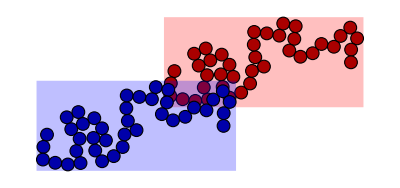

```mathematica
Block[{posA=positions,posB=TranslationTransform[{-10,-5}]@positions,bbA,bbB},

bbA=axesAlignedBoundingBoxes[posA];
bbB=axesAlignedBoundingBoxes[posB];

pairWiseAxesAlignedIntersection[bbA,bbB]//Echo;

Graphics[MapThread[chainGraphic,{{posA,posB},{bbA,bbB},{Red,Blue}}]]

]
```

Next, we only keep points on each chain in the overlap region

```mathematica
returnPointsInOverlap[{positionsA_,{{xMinA_,xMaxA_},{yMinA_,yMaxA_}}},{positionsB_,{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}}]:=With[
{
xMin=Max[xMinA,xMinB],yMin=Max[yMinA,yMinB],
xMax=Min[xMaxA,xMaxB],yMax=Min[yMaxA,yMaxB]
},
Table[Select[pos,xMax>#[[1]]>xMin&&yMax>#[[2]]>yMin&],{pos,{positionsA,positionsB}}]
]
```

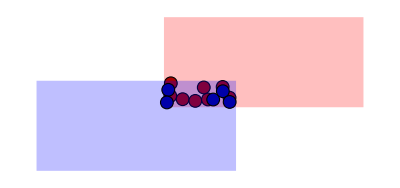

```mathematica
Block[{posA=positions,posB=TranslationTransform[{-10,-5}]@positions,bbA,bbB},

bbA=axesAlignedBoundingBoxes[posA];
bbB=axesAlignedBoundingBoxes[posB];

{posA,posB}=returnPointsInOverlap[{posA,bbA},{posB,bbB}];

Graphics[MapThread[chainGraphic,{{posA,posB},{bbA,bbB},{Red,Blue}}]]

]
```

If the two chains are non-empty, we check pairwise distances

albeit faster than Distance Matrix

```mathematica
shortestDistanceLessThanOne[posA_,posB_]:=Block[{nf=Nearest[posA->"Distance"],i=1,d=2.,l=Length[posB]},
While[d>1. && i<=l,
d=First[nf[posB[[i]]]];
i++
];
d<1.
]
```

Yup. But, useful to document.

```mathematica
RepeatedTiming[Union[Flatten[DistanceMatrix[positions]]][[2]]]
```

{0.000341555,1.}

```mathematica
With[{lists = TakeDrop[positions,Round[Length[positions]/2]]},
RepeatedTiming[shortestDistanceLessThanOne@@lists]]
```

{0.0000102068,False}

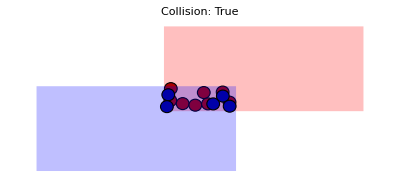

```mathematica
Block[{posA=positions,posB=TranslationTransform[{-10,-5}]@positions,bbA,bbB,collision},

bbA=axesAlignedBoundingBoxes[posA];
bbB=axesAlignedBoundingBoxes[posB];

{posA,posB}=returnPointsInOverlap[{posA,bbA},{posB,bbB}];
collision=If[Length[posA]==0||Length[posB]==0,False,shortestDistanceLessThanOne[posA,posB]];

Graphics[MapThread[chainGraphic,{{posA,posB},{bbA,bbB},{Red,Blue}}],PlotLabel->StringTemplate["Collision: `1`"][collision]]

]
```

Ideally, we’d take temporal coherence into account

I.e. from one frame to another, the connectivity matrix is not likely to change that much

For now, we create the upper-triangular connectivity matrix at each step..

```mathematica
Clear[connectivityMatrixIndex,connectivityMatrix]
connectivityMatrixIndex[bbs_,{i_,j_}]:=pairWiseAxesAlignedIntersection[bbs[[i]],bbs[[j]]]//Boole

connectivityMatrix[bbs_]:=Block[{s=Subsets[Range[Length[bbs]],{2}],l=Length[bbs],is},
SparseArray[s->(connectivityMatrixIndex[bbs,#]&/@s),{l,l}]
]
```

Curious why you are using Graphs?  It would be easier if three regions overlap?

Connectivity Matrix  (0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

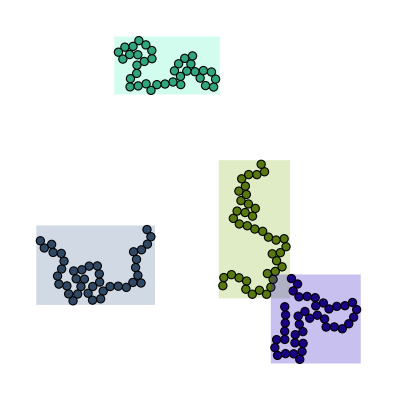

```mathematica
(*SeedRandom[1111];*)
SeedRandom[1111111];
listOfPositions=Table[collisionFreeCorrelatedPolymerChain2D[40,0.3,RandomReal[{-20,20},2]],4];
bbs=axesAlignedBoundingBoxes/@listOfPositions;
cols=RandomColor[4];
Echo[MatrixForm[connectivityMatrix[bbs]],"Connectivity Matrix"];
graphicMultiple=Graphics[MapThread[chainGraphic,{listOfPositions,bbs,cols}]]
```

Wrapping it all together

```mathematica
pairwiseChainCollisionQ[{listOfPositions_,bbs_},{i_,j_}]:=Block[{
posA=listOfPositions[[i]],bbA=bbs[[i]],
posB=listOfPositions[[j]],bbB=bbs[[j]]
},

{posA,posB}=returnPointsInOverlap[{posA,bbA},{posB,bbB}];
If[Length[posA]==0||Length[posB]==0,False,shortestDistanceLessThanOne[posA,posB]]
]

collisionsFreeChainsQ[listOfPositions_]:=Block[{
bbs=axesAlignedBoundingBoxes/@listOfPositions,
mij,nonzero},

mij=connectivityMatrix[bbs];
nonzero=mij["NonzeroPositions"];


NoneTrue[nonzero,pairwiseChainCollisionQ[{listOfPositions,bbs},#]&]

]

moveAllChains[listOfPositions_,ds_]:= Block[{listOfPos=listOfPositions},
listOfPos=moveSingleChain[#,ds]&/@listOfPos;
If[collisionsFreeChainsQ[listOfPos],listOfPos,listOfPositions]
]
```

```mathematica
Dynamic[graphicMultiple]
```

```mathematica
Do[listOfPositions=moveAllChains[listOfPositions,.1];
bbs=axesAlignedBoundingBoxes/@listOfPositions;
graphicMultiple=Graphics[MapThread[chainGraphic,{listOfPositions,bbs,cols}]];
Pause[0.01],
{10000}]
```

$Aborted